```mathematica
(*HVEDM AdS case*)
```

1<=z<2 case

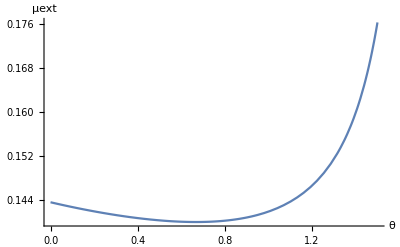

z>2 case

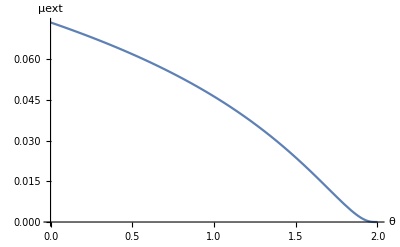

```mathematica
Block[
{μextreme},
μextreme[rh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]rh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
Print["1<=z<2 case"];
Print[Plot[μextreme[0.1,1.75,θ],{θ,0,1.5},AxesLabel->{θ,μext},AxesOrigin->{0,0},PlotRange->All]];
Print["z>2 case"];
Print[Plot[μextreme[0.1,3,θ],{θ,0,2},AxesLabel->{θ,μext},AxesOrigin->{0,0},PlotRange->All]];
]
```

```mathematica
Reduce[
(0≤θ≤2(z-1)&&1≤z<2)||(0≤θ<2&&z≥2),{θ,z}
]
```

0≤θ<2&&z≥(2+θ)/2

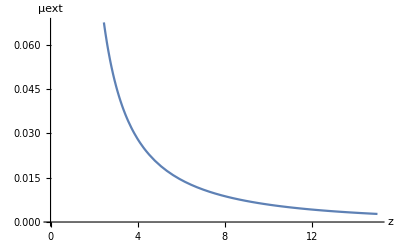

```mathematica
Block[
{μextreme},
μextreme[rh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]rh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
Print[Plot[μextreme[0.1,z,1],{z,1.5,15},AxesLabel->{z,μext},AxesOrigin->{0,0}]];
]
```

```mathematica
(*BI AdS case plots*)
```

```mathematica
Sqrt[1/γ((1+(6-β^2)γ)^2-1)]//OutputForm
```

2    2
     -1 + (1 + (6 - β ) γ)
Sqrt[----------------------]
               γ

```mathematica
Reduce[Sqrt[1/γ((1+(6-β^2)γ)^2-1)]∈Reals&&β≥0&&γ≥0,{β,γ}]
```

(0≤β≤√6&&γ≥0)||(β>√6&&γ≥2/(-6+β^2))

```mathematica
Reduce[Sqrt[1/γ((1+(6-β^2)γ)^2-1)]∈Reals&&β≥0&&γ≥0,{γ,β}]
```

(γ==0&&0≤β≤√6)||(γ>0&&(0≤β≤√6||β≥√2 √((1+3 γ)/γ)))

0<=β<=Sqrt[6] case

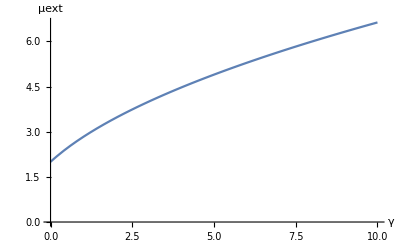

β>Sqrt[6] case

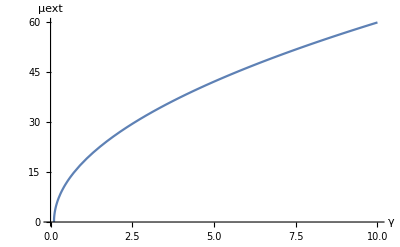

Branch cut 0<=β<=Sqrt[6]

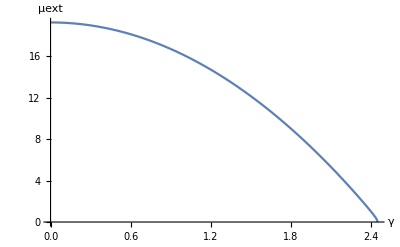

Branch cut β≥ √((2 (1 + 3 γ))/γ)

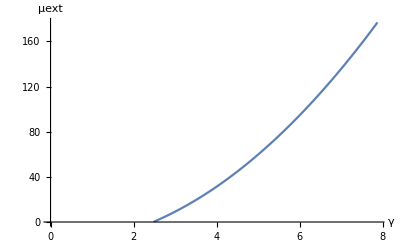

```mathematica
Block[
{μextreme,βTest},
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
Print["0<=β<=Sqrt[6] case"];
Print[Plot[μextreme[2,γ],{γ,0,10},AxesLabel->{γ,μext},AxesOrigin->{0,0}]];
Print["β>Sqrt[6] case"];
Print[Plot[μextreme[5,γ],{γ,2/(5^2-6),10},AxesLabel->{γ,μext},AxesOrigin->{0,0}]];
Print["Branch cut 0<=β<=Sqrt[6]"];
Print[Plot[μextreme[β,10],{β,0,Sqrt[6]},AxesLabel->{γ,μext},AxesOrigin->{0,0}]];
Print["Branch cut β≥ √((2 (1 + 3 γ))/γ)"];
Print[Plot[μextreme[β,10],{β,Sqrt[2(1+3γ)/γ]/.{γ->10},Sqrt[20(1+3γ)/γ]/.{γ->10}},AxesLabel->{γ,μext},AxesOrigin->{0,0}]];
]
```

```mathematica
(* GBAdS plots*)
```

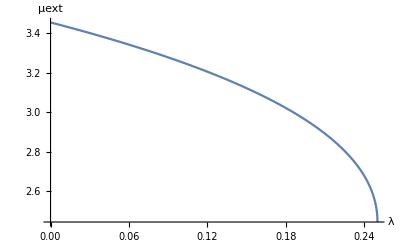

```mathematica
Block[
{μextreme},
μextreme[l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/Sqrt[8 Pi]/l/zh;
Print[Plot[μextreme[1,0.1,λ],{λ,0,1/4},AxesLabel->{λ,μext}]];
]
```